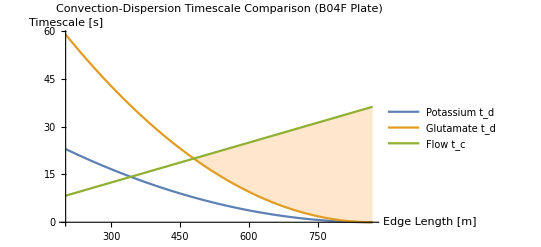

Biofilm diameter (L) and separation (a) in B04F Before TA Dispersive Coupling Begins (T=30C)

Potassium~Convection L=342.167 [um] a=1055.67 [um]

Glutamate~Convection L=479.739 [um] a=780.522 [um]

```mathematica
ClearAll["Global`*"];
(*Calculations based off of Bae et al. 2009*)
Dp0= 1.98*10^-9 *10^12; (*30C potassium diffusion constant [um^2/s](Friedman 1955)*)
Dg0 = 7.72 * 10^-10*10^12;(*30C Glutamate diffusion constant [um^2/s](Rusakov 2011)*)
u=24; (*Flow velocity [um/s]*)
amax=1.34*10^3; (*Max separation between nearest trap edges [um]*)
lmin=200; (*Minimum trap edge length, equivalent to biofilm diameter [um]*)
lmax=amax/2+lmin; (*Maximum trap edge length, equivalent to biofilm diameter [um]*)
a[l_]=amax-2*(l-lmin);
td[l_,D0_]=a[l]^2/(4*π^2*D0); (*Taylor aris dispersion timescale in rectangular channel [s]*)
tc[l_]=l/u;
Plot[{td[l,Dp0],td[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"Convection-Dispersion Timescale Comparison (B04F Plate)",PlotLegends->{"Potassium t_d","Glutamate t_d","Flow t_c"},AxesLabel->{"Edge Length [m]","Timescale [s]"},Filling->{2->{{3},{LightOrange,White}}}]
lsolp =FullSimplify[Solve[td[l,Dp0]==tc[l],l]][[1]];
lsolg =FullSimplify[Solve[td[l,Dg0]==tc[l],l]][[1]];
Print["Biofilm diameter (L) and separation (a) in B04F Before TA Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolp, " [um]", " a=",a[l]/.lsolp, " [um]"]
Print["Glutamate~Convection L=",l/.lsolg, " [um]", " a=",a[l]/.lsolg, " [um]"]
```

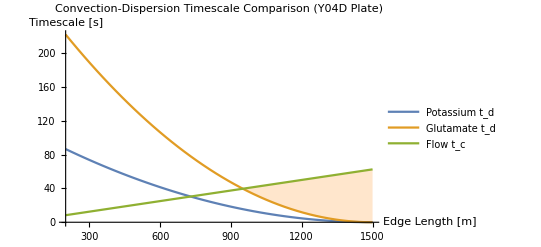

Biofilm diameter (L) and separation (a) in Y04D Before TA Dispersive Coupling Begins (T=30C)

Potassium~Convection L=729.364 [um] a=1541.27 [um]

Glutamate~Convection L=950.636 [um] a=1098.73 [um]

```mathematica
ClearAll["Global`*"];
(*Calculations based off of Bae et al. 2009*)
Dp0= 1.98*10^-9 *10^12; (*30C potassium diffusion constant [um^2/s](Friedman 1955)*)
Dg0 = 7.72 * 10^-10*10^12;(*30C Glutamate diffusion constant [um^2/s](Rusakov 2011)*)
u=24; (*Flow velocity [um/s]*)
lmin=200; (*Minimum trap radius length [um]*)
amax=3*10^3-2*lmin; (*Max separation between nearest trap edges [um]*)
lmax=amax/2+lmin; (*Maximum trap edge length, equivalent to biofilm diameter [um]*)
a[l_]=amax-2*(l-lmin);
td[l_,D0_]=a[l]^2/(4*π^2*D0); (*Taylor aris dispersion timescale in rectangular channel [s]*)
tc[l_]=l/u;
Plot[{td[l,Dp0],td[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"Convection-Dispersion Timescale Comparison (Y04D Plate)",PlotLegends->{"Potassium t_d","Glutamate t_d","Flow t_c"},AxesLabel->{"Edge Length [m]","Timescale [s]"},Filling->{2->{{3},{LightOrange,White}}}]
lsolp =FullSimplify[Solve[td[l,Dp0]==tc[l],l]][[1]];
lsolg =FullSimplify[Solve[td[l,Dg0]==tc[l],l]][[1]];
Print["Biofilm diameter (L) and separation (a) in Y04D Before TA Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolp, " [um]", " a=",a[l]/.lsolp, " [um]"]
Print["Glutamate~Convection L=",l/.lsolg, " [um]", " a=",a[l]/.lsolg, " [um]"]
```

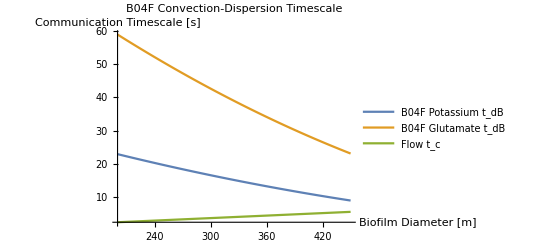

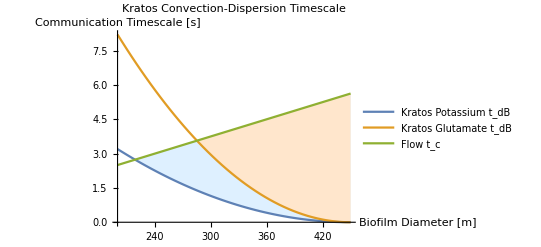

Biofilm Sizes in B04F Before Dispersive Coupling Begins (T=30C)

Potassium~Convection L=515.235 [um] a=709.529 [um]

Glutamate~Convection L=625.854 [um] a=488.292 [um]

Biofilm Sizes in Kratos Before Dispersive Coupling Begins (T=30C)

Potassium~Convection L=218.809 [um] a=462.381 [um]

Glutamate~Convection L=285.191 [um] a=329.618 [um]

```mathematica
ClearAll["Global`*"];
(*Calculations based off of Bae et al. 2009*)
Dp0= 1.98*10^-9 *10^12; (*30C potassium diffusion constant [um^2/s](Friedman 1955)*)
Dg0 = 7.72 * 10^-10*10^12;(*30C Glutamate diffusion constant [um^2/s](Rusakov 2011)*)
u=80; (*Flow velocity [um/s]*)
amaxB=1.34*10^3; (*Max B04F separation between nearest trap edges [um]*)
amaxK=0.5*10^3; (*Max Kratos separation between nearest trap edges [um]*)
lmin=200; (*Minimum trap edge length [um]*)
lmax=amaxK/2+lmin; (*Maximum trap edge length [um], comparing just over Kratos range*)

a[amax_,l_]=amax-2*(l-lmin);
tdB[l_,D0_]=(a[amaxB,l]^2/(4*π^2*D0));
tdK[l_,D0_]=(a[amaxK,l]^2/(4*π^2*D0));
tc[l_]=(l/u);
scaledB[l_,D0_]=tdB[l,D0]*(tdB[lmin,D0])^-1;
scaledK[l_,D0_]=tdK[l,D0]*(tdK[lmin,D0])^-1;
scaletc[l_]=tc[l]*(tc[lmax])^-1;

NormtdB[l_,D0_]=tdB[l,D0]*(Integrate[tdB[l,D0],{l,lmin,lmax}])^-1;
NormtdK[l_,D0_]=tdK[l,D0]*(Integrate[tdK[l,D0],{l,lmin,lmax}])^-1;
Normtc[l_]=tc[l]*(Integrate[tc[l],{l,lmin,lmax}])^-1;

Plot[{tdB[l,Dp0],tdB[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"B04F Convection-Dispersion Timescale",PlotLegends->{"B04F Potassium t_dB","B04F Glutamate t_dB","Flow t_c"},AxesLabel->{"Biofilm Diameter [m]","Communication Timescale [s]"},Filling->{2->{{3},{LightOrange,White}},1->{{3},{LightBlue,White}}}]
Plot[{tdK[l,Dp0],tdK[l,Dg0],tc[l]},{l,lmin,lmax},PlotRange->All,PlotLabel->"Kratos Convection-Dispersion Timescale",PlotLegends->{"Kratos Potassium t_dB","Kratos Glutamate t_dB","Flow t_c"},AxesLabel->{"Biofilm Diameter [m]","Communication Timescale [s]"},Filling->{2->{{3},{LightOrange,White}},1->{{3},{LightBlue,White}}}]

lsolpB =FullSimplify[Solve[tdB[l,Dp0]==tc[l],l]][[1]];
lsolgB =FullSimplify[Solve[tdB[l,Dg0]==tc[l],l]][[1]];
Print["Biofilm Sizes in B04F Before Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolpB, " [um]" ," a=",a[amaxB,l]/.lsolpB, " [um]"]
Print["Glutamate~Convection L=",l/.lsolgB, " [um]" ," a=",a[amaxB,l]/.lsolgB, " [um]"]
lsolpK =FullSimplify[Solve[tdK[l,Dp0]==tc[l],l]][[1]];
lsolgK =FullSimplify[Solve[tdK[l,Dg0]==tc[l],l]][[1]];
Print["Biofilm Sizes in Kratos Before Dispersive Coupling Begins (T=30C)"]
Print["Potassium~Convection L=",l/.lsolpK, " [um]"," a=",a[amaxK,l]/.lsolpK, " [um]"]
Print["Glutamate~Convection L=",l/.lsolgK, " [um]"," a=",a[amaxK,l]/.lsolgK, " [um]"]
```